### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/SeasonalResourceCompetition

### Keywords

example

Details

# Seasonal Resource Competition

Competition for a single resource in an environment that periodically alternates between growing and dying seasons.  A trade-off between growth rate at high and low resource levels can permit coexistence of two species.

The dynamics of the resource (R) and two species (n1 & n2) have two distinct modes:

where τ is the period and ϕ is the proportion of each period where growth is possible and

```mathematica
Needs["EcoEvo`"];
```

Set up the model.

```mathematica
SetModel[{
Pop[n1]->{Equation:>dn1},
Pop[n2]->{Equation:>dn2},
Aux[R]->{Equation:>dR},
Period:>τ}];

dn1:=n1[t]*(Piecewise[{{f1[R[t]]-m,Mod[t,τ]<ϕ τ},{-m,Mod[t,τ]≥ϕ τ}}]);
dn2:=n2[t]*(Piecewise[{{f2[R[t]]-m,Mod[t,τ]<ϕ τ},{-m,Mod[t,τ]≥ϕ τ}}]);
dR:=(Rin-R[t])-Piecewise[{{f1[R[t]]*n1[t]+f2[R[t]]*n2[t],Mod[t,τ]<ϕ τ},{0,Mod[t,τ]≥ϕ τ}}];

f1[R_]:=μ1*R/(R+h1);
f2[R_]:=μ2*R/(R+h2);
```

Set parameter values and plot growth vs resource curves:

```mathematica
μ1=1;μ2=2;
h1=1;h2=4;
ϕ=0.6;
τ=100;
Rin=20;
m=0.2;
```

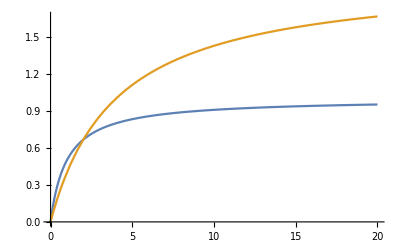

```mathematica
Plot[{f1[R],f2[R]},{R,0,Rin}]
```

Simulate the dynamics for three periods:

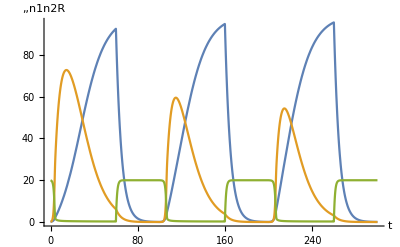

```mathematica
sol=EcoSim[{n1->0.1,n2->0.1,R->Rin},3τ];
PlotDynamics[sol]
```

Find monoculture limit cycles for each species and calculate invasion rates to verify stable coexistence.

Species 2 invading species 1:

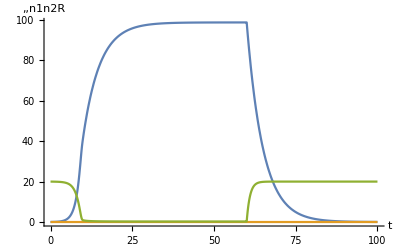

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {60.1547}. NIntegrate obtained 1.8108 and 0.00222528 for the integral and error estimates.

0.018108

```mathematica
eq1=FindEcoCycle[{n1->0.1,R->Rin}];
PlotDynamics[eq1]
Inv[eq1,n2]
```

Species 1 invading species 2:

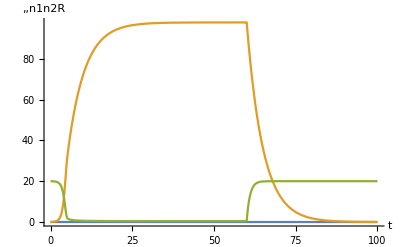

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {60.1547}. NIntegrate obtained 2.75081 and 0.00361845 for the integral and error estimates.

0.0275081

```mathematica
eq2=FindEcoCycle[{n2->0.1,R->Rin}];
PlotDynamics[eq2]
Inv[eq2,n1]
```

Since each species can invade a monoculture of the other, the two species coexist.  We can find the two-species coexistence limit cycle:

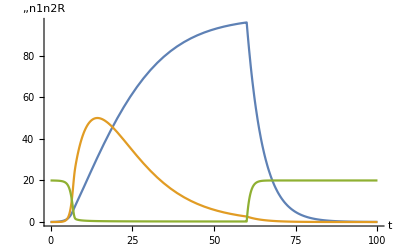

```mathematica
eq=FindEcoCycle[FinalSlice[sol]];
PlotDynamics[eq]
```

We can verify its stability by calculating its Floquet exponents with EcoEigenvalues:

```mathematica
EcoEigenvalues[eq]
```

{-0.00789932,-0.120309,-∞}

We can plot the invasion rates of versus ϕ to see where species coexist and where one outcompetes the other.

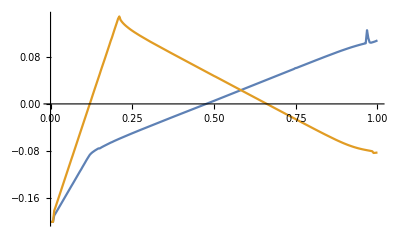

```mathematica
(* 185 sec *)
Clear[ϕ];
Plot[{Inv[FindEcoAttractor[{n2->0.1,R->Rin}],n1],Inv[FindEcoAttractor[{n1->0.1,R->Rin}],n2]},{ϕ,0,1},PlotPoints->5]//Quiet
```

Verify coexistence region with some more illustrative simulations.

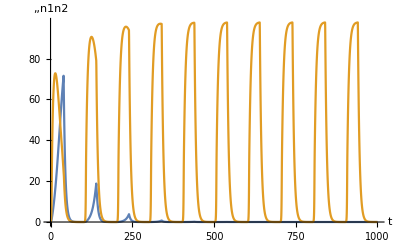

```mathematica
ϕ=0.4;
sol=EcoSim[{n1->0.1,n2->0.1,R->Rin},10τ];
PlotDynamics[sol,{n1,n2}]
```

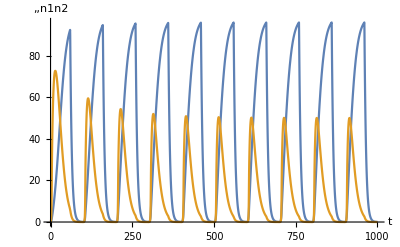

```mathematica
ϕ=0.6;
sol=EcoSim[{n1->0.1,n2->0.1,R->Rin},10τ];
PlotDynamics[sol,{n1,n2}]
```

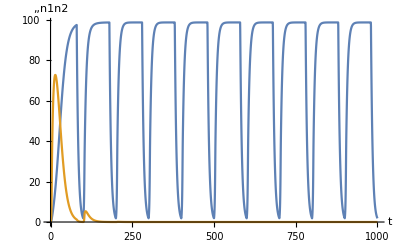

```mathematica
ϕ=0.8;
sol=EcoSim[{n1->0.1,n2->0.1,R->Rin},10τ];
PlotDynamics[sol,{n1,n2}]
```

## References

Litchman E, Klausmeier CA. 2001. Competition of phytoplankton under fluctuating light.  American Naturalist 157: 170-187.  similar model

More About

Related Tutorials

ExampleModels

Related Wolfram Education Group Courses